```mathematica
taps = Import["/home/john/Code/mathematica/dsp/taps.dat"];
```

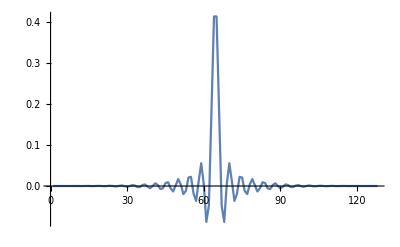

```mathematica
ListLinePlot[Flatten@taps,PlotRange->All]
```

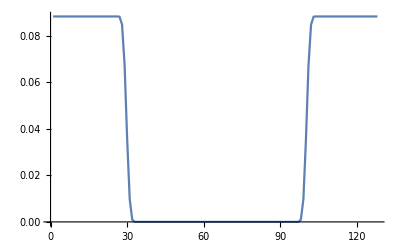

```mathematica
ListLinePlot[Abs@Fourier@Flatten@taps,PlotRange->All]
```

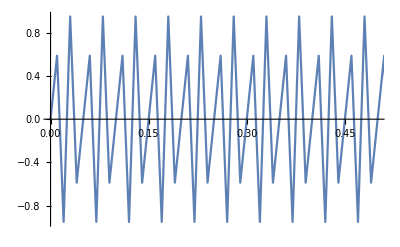

```mathematica
ListLinePlot[Table[Sin[40*2*Pi*x],{x,0,2Pi,.01}],DataRange->{0,2Pi},PlotRange->{{0,1/2},All}]
```

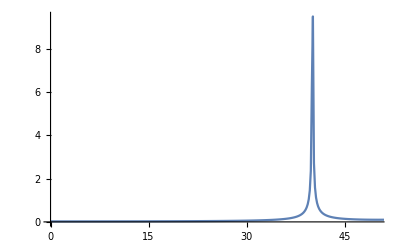

```mathematica
ListLinePlot[Abs@Fourier@Table[Sin[40*2*Pi*x],{x,0,2Pi,.01}],DataRange->{0,100},PlotRange->{{0,50},All}]
```

```mathematica
data = Table[Sin[20*2*Pi*n]+Sin[600*2*Pi*n],{n,0,4Pi,1/2400}];
```

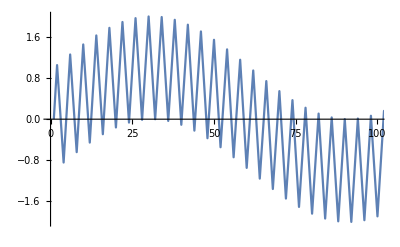

```mathematica
ListLinePlot[data,PlotRange->{{0,100},All}]
```

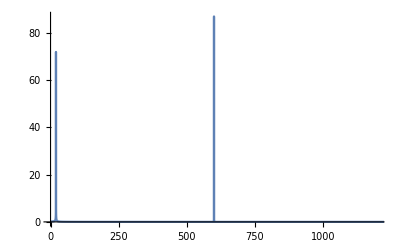

```mathematica
ListLinePlot[Abs@Fourier@data,DataRange->{0,2400},PlotRange->{{0,1200},All}]
```

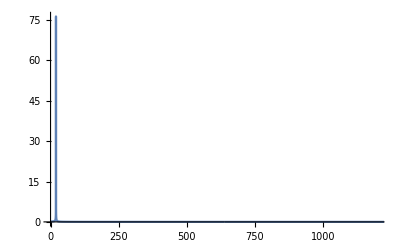

```mathematica
ListLinePlot[Abs@Fourier@ListConvolve[Flatten@taps, Flatten@data],DataRange->{0,2400},PlotRange->{{0,1200},All}]
```